# Deterministic

```mathematica
Quit
```

```mathematica
nb1=NotebookOpen[FileNameJoin[{NotebookDirectory[],"Common.nb"}]];
SelectionMove[nb1,All,Notebook]
SelectionEvaluate[nb1]
SetSelectedNotebook[EvaluationNotebook[]];
```

```mathematica
<<MaTeX`
SetDirectory[NotebookDirectory[]];
```

```mathematica
threshold=10^-3;

(*requires γ*)
EG[W_,zstart_,nIterations_]:=Module[{
V,
iterates=Table[Q[zstart],{nIterations}],
Hzdiffs=Table[Q[zstart],{nIterations}],
z=Q[zstart],
zbar=Q[zstart],
Hz,Hzbar,Hzdiff},
V[vec_]:=W@@vec;
Do[
If[Norm[V[z]]<threshold,iterates[[n]]=zbar;Hzdiffs[[n]]=Hzdiff,
iterates[[n]]=zbar;
Hz=z-γ*V[z];
zbar=Q[Hz];
Hzbar=zbar-γ*V[zbar];
Hzdiff=Hzbar-Hz;
Hzdiffs[[n]]=Hzdiff;
z=z+(Hzdiff)],
{n,nIterations}];
{iterates,Hzdiffs}]

(*requires γ and α*)
EGPlus[W_,zstart_,nIterations_]:=Module[{
V,
iterates=Table[Q[zstart],{nIterations}],
Hzdiffs=Table[Q[zstart],{nIterations}],
z=Q[zstart],
zbar=Q[zstart],
Hz,Hzbar,Hzdiff},
V[vec_]:=W@@vec;
Do[
If[Norm[V[z]]<threshold,iterates[[n]]=zbar;Hzdiffs[[n]]=Hzdiff,
iterates[[n]]=zbar;
Hz=z-γ*V[z];
zbar=Q[Hz];
Hzbar=zbar-γ*V[zbar];
Hzdiff=Hzbar-Hz;
Hzdiffs[[n]]=Hzdiff;
z=z+λ*α*(Hzdiff)],
{n,nIterations}];
{iterates,Hzdiffs}]

(*requires σ,γ and λ*)
AdaptiveEGPlus[W_,zstart_,nIterations_]:=Module[{
α,V,
iterates=Table[Q[zstart],{nIterations}],
Hzdiffs=Table[Q[zstart],{nIterations}],
z=Q[zstart],
zbar=Q[zstart],
Hz,Hzbar,Hzdiff},
V[vec_]:=W@@vec;
Do[
If[Norm[V[z]]<threshold,iterates[[n]]=zbar;Hzdiffs[[n]]=Hzdiff,
iterates[[n]]=zbar;
Hz=z-γ*V[z];
zbar=Q[Hz];
Hzbar=zbar-γ*V[zbar];
Hzdiff=Hzbar-Hz;
Hzdiffs[[n]]=Hzdiff;
α=Evaluate@(σ/γ+((zbar-z).(Hzdiff))/(Total[(Hzdiff)^2]));
z=z+λ*α*(Hzdiff)],
{n,nIterations}];
{iterates,Hzdiffs}]

Linesearch[W_,z_,γ0_,ν_,τ_]:=Module[{V,G,γ,i},
γ=γ0;
i=0;
V[vec_]:=W@@vec;
G[vec_]:=Q[z-γ*V[z]];
While[γ*Norm[V[G[z]]-V[z]]>ν*Norm[G[z]-z],
γ*=τ;i++];
{γ,i}
];

(*requires λ and τ, ν*)
CurvatureEGPlus[W_,zstart_,nIterations_]:=Module[{
J,α,σ,γ,i,γ0,Lips,V,
iterates=Table[Q[zstart],{nIterations}],
Hzdiffs=Table[Q[zstart],{nIterations}],
z=Q[zstart],
zbar=Q[zstart],
Hz,Hzbar,Hzdiff},
linesearchSteps=Table[0,{nIterations}];
V[vec_]:=W@@vec;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
Lips[x_,y_]:=Evaluate@(SingularValueList[J[x,y],1][[1]]);
Do[
If[Norm[V[z]]<threshold,iterates[[n]]=zbar;Hzdiffs[[n]]=Hzdiff,
γ0=ν/Re[Lips[z[[1]],z[[2]]]];
{γ,linesearchSteps[[n]]}=Linesearch[W,z,γ0,ν,τ];
σ=-γ/2*0.99;
iterates[[n]]=zbar;
Hz=z-γ*V[z];
zbar=Q[Hz];
Hzbar=zbar-γ*V[zbar];
Hzdiff=Hzbar-Hz;
Hzdiffs[[n]]=Hzdiff;
α=Evaluate@(σ/γ+((zbar-z).(Hzdiff))/(Total[(Hzdiff)^2]));
z=z+λ*α*(Hzdiff)],
{n,nIterations}];
{iterates,Hzdiffs}]

numTotalIterates=50;
plotIterates[W_,iterates_,legends_]:=Module[{},
Print[Length[iterates]];
iteratesReduces=Map[ArrayResample[#,numTotalIterates]&,iterates];
legend=If[Length[legends]≠0,ListLinePlot[iteratesReduces,
PlotMarkers->Automatic,
Joined->True,
PlotLegends->Placed[legends,Below]][[2]],{}];
lines=ListLinePlot[iterates,PlotLegends->legend];
markers=ListLinePlot[iteratesReduces,
PlotMarkers->Automatic,
Joined->False];
Show[
plotFlow[W,side],
lines,
markers,
Frame->True]];

legends={"CEG","CEG+","AdaptiveEG+","CurvatureEG+"};
plotAllDeteterministicMethods[W_]:=Module[{},
EGPlusIterates=EGPlus[W,init,T];
EGIterates=EG[W,init,T];
CurvatureEGPlusIterates=CurvatureEGPlus[W,init,T];
AdaptiveEGPlusIterates=AdaptiveEGPlus[W,init,T];
iterates=Map[First,{EGIterates,EGPlusIterates,AdaptiveEGPlusIterates,CurvatureEGPlusIterates}];
plotIterates[W,iterates,legends]]
```

## Forsaken

```mathematica
boundary=3/2;
side=3/2;
$Assumptions=x∈Reals&&y∈Reals;
Q[z_]:=Clip[z,{-boundary,boundary}];

phi[z_]:=z^2/4-z^4/2+z^6/6
Forsaken[x_,y_]:=x (y-0.45)+phi[x]-phi[y]
W[x_,y_]:=Evaluate@getW[Forsaken];

padding=0.3;
initialPointData=Flatten[
Table[
{x,y},
{x,-boundary+padding,boundary-padding,0.75},
{y,- boundary+padding,boundary-padding,0.75}],1];
Length[initialPointData]
```

16

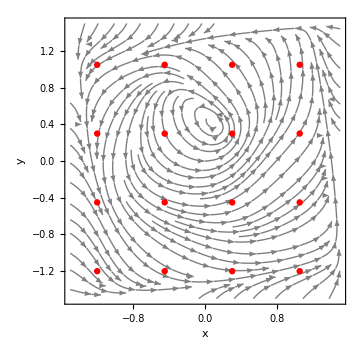

```mathematica
Show[plotFlow[W,side],
ListPlot[initialPointData,PlotStyle->Red]]
```

## Finding Lipschitz

```mathematica
cons=-boundary<=x≤boundary&&-boundary<=y<=boundary;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
LocalLips[x_,y_]:=Evaluate@Norm[J[x,y],2];
```

```mathematica
L=Assuming[{x∈Reals,y∈Reals},MaxValue[{
LocalLips[x,y],cons},{x,y}]//Simplify]
N[-1/(2L)]
```

1/80 √(1/2 (993841+1089 √801761))

-0.0403142

## EG+ and CurvatureEG+

```mathematica
T=500;
α=1/2;
λ=1;
σ=-γ/2*0.99;
γ=1/L;
```

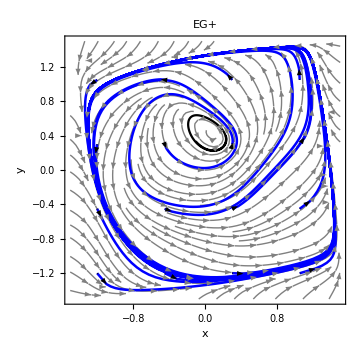

Figs/Forsaken_EG+.png

```mathematica
k=10;K=25;
Wreverse[x_,y_]:=-W[x,y];
sol=SolveFlow[Wreverse,{0.2,0.5},T];
iterates=Table[EGPlus[W,init,T][[1]],{init,initialPointData}];
prox=Table[
Graphics[
Append[{Blue,Thickness->0.005},Line[orbit[[;;;;1]],VertexColors->{Blue,Blue}]]],
{orbit,iterates}];
starts2=Map[Take[#,2]&,iterates];
Show[plotFlow[W,side],prox,
Graphics[{Dashing[{0,1000}],Arrowheads[{0.04,-0}],Arrow[starts2]}],ParametricPlot[{w1[t],w2[t]}/.sol,{t,K-k,K},PlotStyle->Black],PlotLabel->"EG+"]
Export["Figs/Forsaken_EG+.png",%]
```

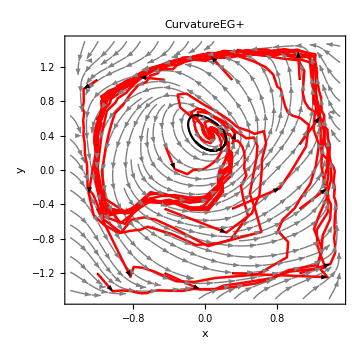

Figs/Forsaken_CurvatureEG+.png

```mathematica
T=200;
α=1/2;
λ=1;
τ=0.8;
ν=0.8;
σ=-γ/2*0.99;
γ=1/L;

k=10;K=25;
Wreverse[x_,y_]:=-W[x,y];
sol=SolveFlow[Wreverse,{0.2,0.5},T];
iterates=Table[CurvatureEGPlus[W,init,T][[1]],{init,initialPointData}];
prox=Table[
Graphics[
Append[{Red,Thickness->0.005},Line[orbit[[;;;;1]],VertexColors->{Red,Red}]]],
{orbit,iterates}];
starts2=Map[Take[#,2]&,iterates];
Show[plotFlow[W,side],prox,
Graphics[{Dashing[{0,1000}],Arrowheads[{0.04,-0}],Arrow[starts2]}],ParametricPlot[{w1[t],w2[t]}/.sol,{t,K-k,K},PlotStyle->Black],PlotLabel->"CurvatureEG+"]
Export["Figs/Forsaken_CurvatureEG+.png",%]
```

4

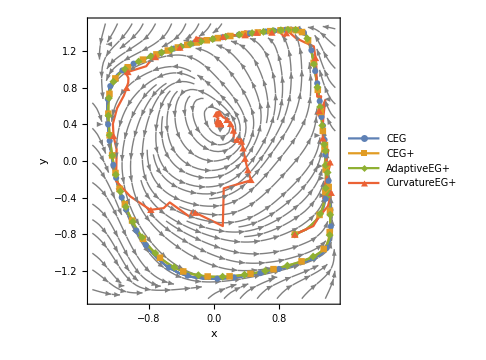

Figs/Forsaken_all.png

```mathematica
init={1.0,-0.8};
T=200;
α=1/2;
λ=1;
τ=0.5;
ν=0.99;
σ=-γ/2*0.99;
γ=1/L;

legends={"CEG","CEG+","AdaptiveEG+","CurvatureEG+"};
plot=plotAllDeteterministicMethods[W]
Export["Figs/Forsaken_all.png",plot]
```

## PolarGame

```mathematica
boundary=11/10;
side=11/10;
$Assumptions=x∈Reals&&y∈Reals;
Q[z_]:=Clip[z,{-boundary,boundary}];
W[x_,y_]:={-b y+1/16 a x (-1+x^2+y^2) (-9+16 x^2+16 y^2),b x+1/16 a y (-1+x^2+y^2) (-9+16 x^2+16 y^2)}
star={0,0};
weakMVIcondition[x_,y_]:=Evaluate@(W[x,y]).({x,y}-star)/Norm[W[x,y]]^2;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
LocalLips[x_,y_]:=Evaluate@Norm[J[x,y],2];

init={1.0,0.5};
T=500;
α=1/2;
λ=1;
τ=0.5;
ν=0.99;
```

4

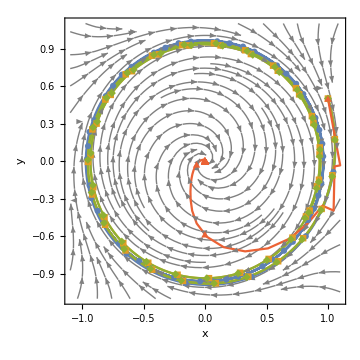

Figs/Det_PolarGame_hard.png

```mathematica
a=1;b=1;
L=(√(70246989617+2538096 √704424929))/20000;
σ=-γ/2*0.99;
γ=1/L;
legends={};
plot=plotAllDeteterministicMethods[W]
Export["Figs/Det_PolarGame_hard.png",plot]
```

4

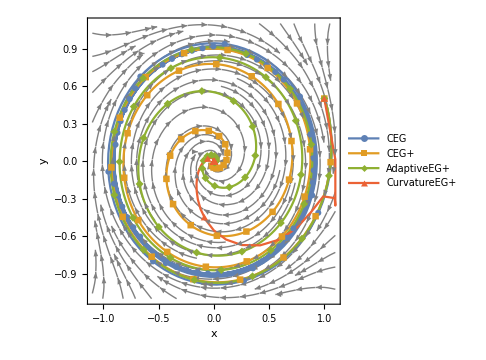

Figs/Det_PolarGame_medium.png

```mathematica
T=600;
init={1.0,0.5};
a=3/4;b=1;
L=(√(635022906553+7614288 √6383574361))/80000;
σ=-γ/2*0.99;
γ=1/L;
legends={"CEG","CEG+","AdaptiveEG+","CurvatureEG+"};
plot=plotAllDeteterministicMethods[W]
Export["Figs/Det_PolarGame_medium.png",plot]
```

4

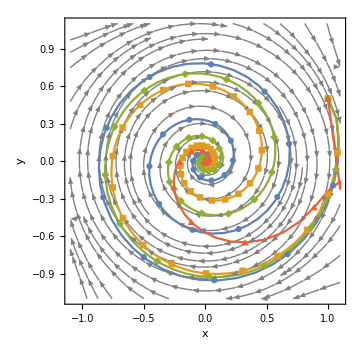

Figs/Det_PolarGame_easy.png

```mathematica
init={1.0,0.5};
T=200;
a=1/3;b=1;
α=1/2;
L=(√(73446989617+2538096 √754424929))/60000;
σ=-γ/2*0.99;
γ=1/L;
legends={};
plot=plotAllDeteterministicMethods[W]
Export["Figs/Det_PolarGame_easy.png",plot]
```

## Lower bound example

```mathematica
Clear[a,b];
c=1/3;
rule=Solve[b+(a c)/(√(1-c^2))==0,a][[1]][[1]]
```

a→-2 √2 b

2 √2

3

{-x+2 √2 y,-2 √2 x-y}

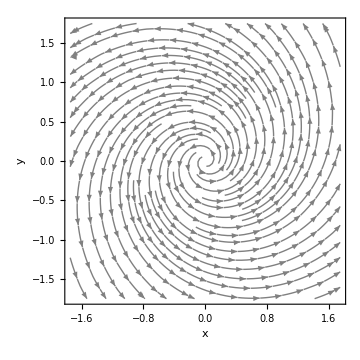

```mathematica
b=-1;
a=a/.rule
L=√(a^2+b^2)
F[x_,y_]:=a*x*y+b/2*x^2-b/2*y^2;
W[x_,y_]:=Evaluate@getW[F];
W[x,y]
plotFlow[W]
```

## All methods on lowerbound example

```mathematica
boundary=11/10;
side=11/10;
$Assumptions=x∈Reals&&y∈Reals;
Q[z_]:=Clip[z,{-boundary,boundary}];
init={1.0,0.5};
T=10000;
α=1/2;
λ=1;
τ=0.5;
ν=0.99;
γ=1/L;
σ=-γ/2*0.99;
threshold=10^-100;
```

```mathematica
(*legends={"CEG","CEG+","AdaptiveEG+","CurvatureEG+"};*)
legends={};
plotAllDeterministicMethodsWithNorm[W_]:=Module[{norms,Hzdiffs},
EGPlusIterates=EGPlus[W,init,T];
EGIterates=EG[W,init,T];
CurvatureEGPlusIterates=CurvatureEGPlus[W,init,T];
AdaptiveEGPlusIterates=AdaptiveEGPlus[W,init,T];
iterates=Map[First,{EGIterates,EGPlusIterates,AdaptiveEGPlusIterates,CurvatureEGPlusIterates}];
Hzdiffs=Map[Last,{EGIterates,EGPlusIterates,AdaptiveEGPlusIterates,CurvatureEGPlusIterates}];
norms=Table[Table[Norm[p],{p,orbit}],{orbit,Hzdiffs}];
iteratePlot=
plotIterates[W,iterates,legends];
Print[iteratePlot];
ListLogPlot[norms,
Frame->True,
FrameLabel->{"k",MaTeX["\\|H\\bar{z}^k-Hz^k\\|"]},
Joined->True,
AspectRatio->1,
PlotLegends->Placed[legends,Below]]]
```

4

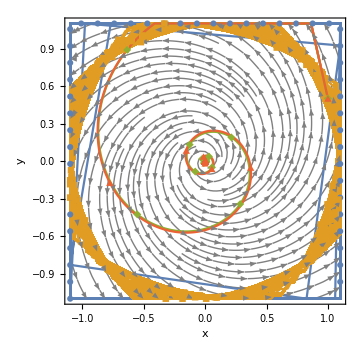

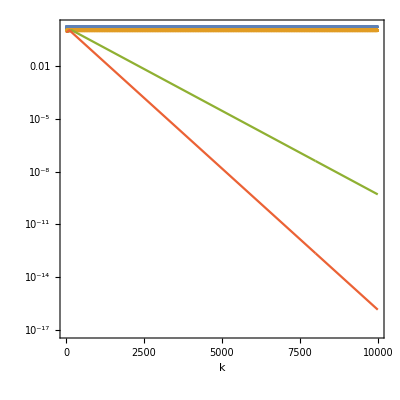

Figs/Det_Bilinear_invc=3_iterates.png

Figs/Det_Bilinear_invc=3.png

```mathematica
plot=plotAllDeterministicMethodsWithNorm[W]
Export["Figs/Det_Bilinear_invc=3_iterates.png",iteratePlot]
Export["Figs/Det_Bilinear_invc=3.png",plot]
```

## CEG+ comparison on Lowerbound

```mathematica
boundary=11/10;
side=11/10;
Q[z_]:=Clip[z,{-boundary,boundary}];
init={1.0,0.5};
T=1000;
α=1/2;
λ=1;
ν=0.99;
γ=1/L;
σ=-γ/2*0.99;
threshold=10^-100;
```

2

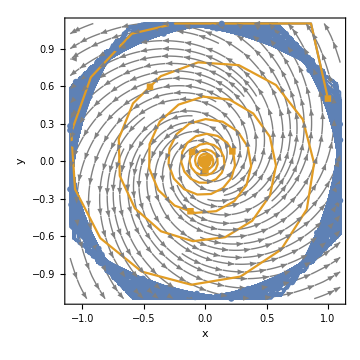

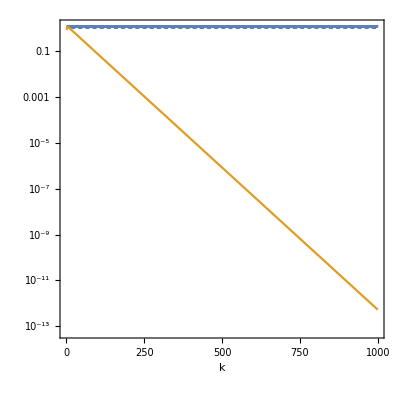

Figs/Det_CEGPlus_comparison.png

```mathematica
(*legends={"CEG","CEG+","AdaptiveEG+","CurvatureEG+"};*)
legends={MaTeX["\\text{CEG+ }(\\bar{\\alpha}_k = 1/2)"],MaTeX["\\text{CEG+ }(\\bar{\\alpha}_k = 1/4)"]};
plotAllDeterministicMethodsWithNorm[W_]:=Module[{norms,Hzdiffs},
α=1/2;
EGPlusIterates=EGPlus[W,init,T];
α=1/4;
EGPlusIterates2=EGPlus[W,init,T];
iterates=Map[First,{EGPlusIterates,EGPlusIterates2}];
Hzdiffs=Map[Last,{EGPlusIterates,EGPlusIterates2}];
norms=Table[Table[Norm[p],{p,orbit}],{orbit,Hzdiffs}];
iteratePlot=
plotIterates[W,iterates,legends];
Print[iteratePlot];
ListLogPlot[norms,
Frame->True,
FrameLabel->{"k",MaTeX["\\|H\\bar{z}^k-Hz^k\\|"]},
Joined->True,
AspectRatio->1,
PlotLegends->Placed[LineLegend[legends,LegendLayout->{"Row",1}],Below]]]
plot=plotAllDeterministicMethodsWithNorm[W]
Export["Figs/Det_CEGPlus_comparison.png",iteratePlot]
```

## GlobalForsaken

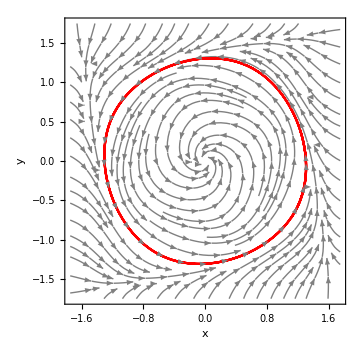

```mathematica
globalphi[z_]:=(z^2/3-z^4/3+z^6 2/21)
GlobalForsaken[x_,y_]:=x *y+globalphi[x]-globalphi[y]
W[x_,y_]:=Evaluate@getW[GlobalForsaken];
plotTrajectory[W,{1,1.0},20,25]
```

```mathematica
(*boundary=18/10;
side=18/10;
Q[z_]:=Clip[z,{-boundary,boundary}];*)
boundary=4/3;
side=4/3;
Q[z_]:=z/Max[1,Norm[z]/side];
$Assumptions=x∈Reals&&y∈Reals;
star={0,0};
weakMVIcondition[x_,y_]:=Evaluate@(W[x,y]).({x,y}-star)/Norm[W[x,y]]^2;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);

init={1.2,1.2};
T=50;
α=1/2;
λ=1;
τ=0.5;ν=0.99;
```

4

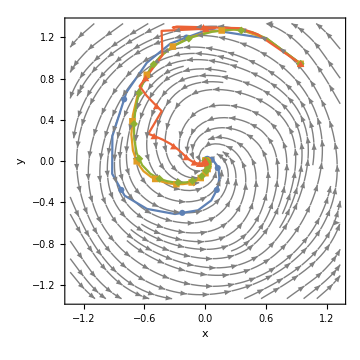

Figs/Det_GlobalForsaken.png

```mathematica
legends={};
L=(√(1/2 (74125591+9409 √59721901)))/2835;
σ=-γ/2*0.99;
γ=1/L;
numTotalIterates=20;
plot=plotAllDeteterministicMethods[W]
Export["Figs/Det_GlobalForsaken.png",plot]
```